```mathematica
(* In the Subscript[χ̃, 1]^± rest frame *)
(* Consider τ to be massless *)
(* Consider decays in the transverse plane only *)
(* p stands for Subscript[p, T] *)
```

```mathematica
ClearAll["Global`*"];
Needs["Notation`"];
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]];
```

```mathematica
Subscript[m, Subscript[t̃, 1]]=400;
Subscript[m, Subscript[χ̃, 1]^0]=100;
x={0.25,0.5,0.75};
θ=0; (* Subscript[p, Subscript[τ, A]] is maximum *)
```

```mathematica
m_(Subscript[χ̃, 1]^±)[Subscript[m, Subscript[t̃, 1]]:_,Subscript[m, Subscript[χ̃, 1]^0]:_,x_]:=Subscript[m, Subscript[χ̃, 1]^0]+0.5(Subscript[m, Subscript[t̃, 1]]-Subscript[m, Subscript[χ̃, 1]^0])
m_(Subscript[χ̃, 1]^±)[Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x]
```

250.

```mathematica
Subscript[m, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]]:_,Subscript[m, Subscript[χ̃, 1]^0]:_,x_]:=Subscript[m, Subscript[χ̃, 1]^0]+0.5x(Subscript[m, Subscript[t̃, 1]]-Subscript[m, Subscript[χ̃, 1]^0])
Subscript[m, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x]
```

{137.5,175.,212.5}

```mathematica
Subscript[p, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]]:_,Subscript[m, Subscript[χ̃, 1]^0]:_,x_]:=((m_(Subscript[χ̃, 1]^±)[Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x])^2-(Subscript[m, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x])^2)/(2 m_(Subscript[χ̃, 1]^±)[Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x])
Subscript[p, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x]
```

{87.1875,63.75,34.6875}

{58.8843,84.1837,97.3183}

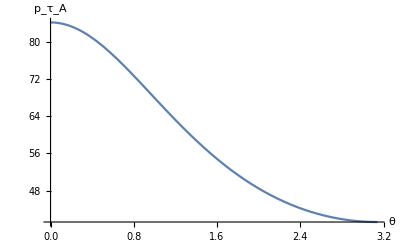

```mathematica
(* Subscript[τ, A] comes from Subscript[χ̃, 1]^±->Subscript[τ̃, 1] Subscript[ν, τ]->τ Subscript[χ̃, 1]^0 Subscript[ν, τ] *)
Subscript[p, Subscript[τ, A]][Subscript[m, Subscript[t̃, 1]]:_,Subscript[m, Subscript[χ̃, 1]^0]:_,x_,θ_]:=((Subscript[m, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x])^2-Subscript[m, Subscript[χ̃, 1]^0]^2)/(2(√((Subscript[m, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x])^2+(Subscript[p, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x])^2)-Subscript[p, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x]Cos[θ]))
Subscript[p, Subscript[τ, A]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ]
Plot[Subscript[p, Subscript[τ, A]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],0.5,θ],{θ,0,π},AxesLabel->{"θ","p_τ_A"}]
```

```mathematica
(* Subscript[τ, B] comes from Subscript[χ̃, 1]^±->τ Subscript[ν̃, τ] *)
Subscript[p, Subscript[τ, B]][Subscript[m, Subscript[t̃, 1]]:_,Subscript[m, Subscript[χ̃, 1]^0]:_,x_]:=Subscript[p, Subscript[τ̃, 1]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x]
Subscript[p, Subscript[τ, B]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x]
```

{87.1875,63.75,34.6875}

```mathematica
(* Average of Subscript[τ, A] and Subscript[τ, B] as they both have equal probability of occurence *)
Subscript[p, τ][Subscript[m, Subscript[t̃, 1]]:_,Subscript[m, Subscript[χ̃, 1]^0]:_,x_,θ]:=(Subscript[p, Subscript[τ, A]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ]+Subscript[p, Subscript[τ, B]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x])/2
Subscript[p, τ][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ]
```

{73.0359,73.9668,66.0029}

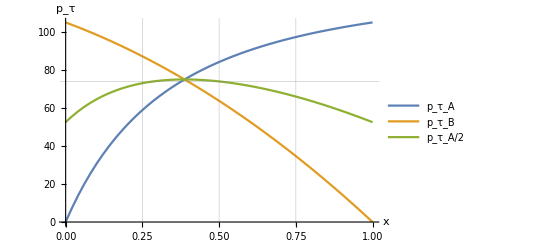

```mathematica
Plot[{Subscript[p, Subscript[τ, A]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ],Subscript[p, Subscript[τ, B]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x],Subscript[p, τ][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ]},{x,0, 1},PlotLegends->{"p_τ_A","p_τ_B","p_τ_A/2"},GridLines->{{0.25,0.5,0.75},{Subscript[p, τ][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],0.5,θ]}},AxesLabel->{"x","p_τ"}]
```

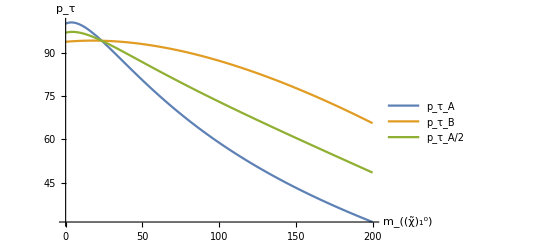

```mathematica
x=0.25;
Plot[{Subscript[p, Subscript[τ, A]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ],Subscript[p, Subscript[τ, B]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x],Subscript[p, τ][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ]},{Subscript[m, Subscript[χ̃, 1]^0],0,Subscript[m, Subscript[t̃, 1]]/2},PlotLegends->{"p_τ_A","p_τ_B","p_τ_A/2"},AxesLabel->{"m_((χ̃)_1^0)","p_τ"}]
```

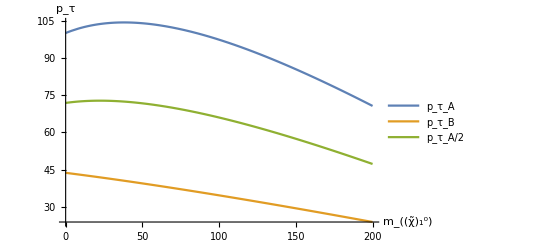

```mathematica
x=0.75;
Plot[{Subscript[p, Subscript[τ, A]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ],Subscript[p, Subscript[τ, B]][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x],Subscript[p, τ][Subscript[m, Subscript[t̃, 1]],Subscript[m, Subscript[χ̃, 1]^0],x,θ]},{Subscript[m, Subscript[χ̃, 1]^0],0,Subscript[m, Subscript[t̃, 1]]/2},PlotLegends->{"p_τ_A","p_τ_B","p_τ_A/2"},AxesLabel->{"m_((χ̃)_1^0)","p_τ"}]
```